# Modeling Epidemic Spread with Compartmental Models

Delete cached data:

```mathematica
DeleteObject[ResourceObject["Epidemic Data for Novel Coronavirus COVID-19"]]
```

Calculate the infected, recovered and deceased population:

```mathematica
{infected,recovered,deceased}=Normal@ResourceData["Epidemic Data for Novel Coronavirus COVID-19","WorldCountries"][SelectFirst[#Country==Entity["Country","SouthKorea"]&],{#ConfirmedCases-(#RecoveredCases+#Deaths),#RecoveredCases,#Deaths}&]
```

{TimeSeries[…],TimeSeries[…],TimeSeries[…]}

Plot the preceding variables:

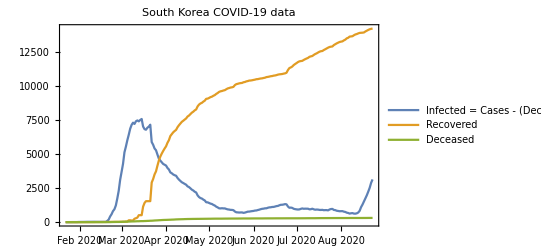

```mathematica
DateListPlot[{infected,recovered,deceased},]
```

Set up infected, recovered and deceased data for the first 100 days:

```mathematica
infectedData=MapIndexed[{#2⟦1⟧,#1}&][infected["Values"]]⟦;;100⟧;
%//Short
```

{{1,1},{2,1},{3,2},{4,2},{5,3},«90»,{96,1731},{97,1654},{98,1593},{99,1459},{100,1454}}

```mathematica
recoveredData=MapIndexed[{#2⟦1⟧,#1}&][recovered["Values"]]⟦;;100⟧;
%//Short
```

{{1,0},{2,0},{3,0},{4,0},{5,0},«90»,{96,8764},{97,8854},{98,8922},{99,9059},{100,9072}}

```mathematica
deceasedData=MapIndexed[{#2⟦1⟧,#1}&][deceased["Values"]]⟦;;100⟧;
%//Short
```

{{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},«88»,{95,242},{96,243},{97,244},{98,246},{99,247},{100,248}}

-Graphics-

𝒮→^(β λ[t])ℐ | infection
ℐ→^γ ℛ | recovery

Set up the differential equations:

```mathematica
odesSIR={𝒮'[t]==-β 𝒮[t] ℐ[t]/𝒩,ℐ'[t]==β 𝒮[t] ℐ[t]/𝒩-γ ℐ[t],ℛ'[t]==γ ℐ[t]};
```

Solve for the parameters:

```mathematica
pmNDSolve=ParametricNDSolve[{odesSIR,𝒮[0]==𝒩-i0,ℐ[0]==i0,ℛ[0]==0},{𝒮,ℐ,ℛ},{t,0,100},{𝒩,i0,β,γ}]
```

{𝒮→ParametricFunction[<>],ℐ→ParametricFunction[<>],ℛ→ParametricFunction[<>]}

```mathematica
{solI,solR}={ℐ,ℛ}/.pmNDSolve
```

{ParametricFunction[<>],ParametricFunction[<>]}

Fit parameters manually:

```mathematica
Manipulate[Plot[{solI[nn,1,beta,gamma][t],solR[nn,1,beta,gamma][t]},{t,0,100},Epilog:>{Blue,Point@infectedData,Orange,Point@recoveredData},],
{{nn,10000,"𝒩"},5000,15000,Appearance->"Labeled"},
{{beta,.26,"β"},0,1,Appearance->"Labeled"},
{{gamma,.034,"γ"},0,.1,Appearance->"Labeled"},SaveDefinitions->True]
```

Prepend 1 as a tag for infected data and 2 for recovered data, then join them:

```mathematica
dataSIR=Join[Prepend[#,1]&/@infectedData,Prepend[#,2]&/@recoveredData];
%//Short
```

{{1,1,1},{1,2,1},{1,3,2},{1,4,2},{1,5,3},«191»,{2,97,8854},{2,98,8922},{2,99,9059},{2,100,9072}}

Define a fitting function for the infected and recovered data separately, depending on their tags (1 and 2):

```mathematica
fitModelSIR[𝒩_,β_,γ_][tag_,t_]:=Which[tag==1,solI[𝒩,1,β,γ][t],tag==2,solR[𝒩,1,β,γ][t]]
```

Fit nonlinear models solI and solR to infected and recovered data, respectively, at the same time:

```mathematica
fitSIR=NonlinearModelFit[dataSIR,fitModelSIR[𝒩,β,γ][tag,t],{{𝒩,12000},{β,0.27},{γ,0.03}},{tag,t}]
```

FittedModel[Which[tag==1,solI[10544.6,1,«20»,0.0293782][t],«1»,solR[10544.6,1,0.243677,0.0293782][t]]]

What does the fit look like visually?

Return a table of fitted parameter information:

```mathematica
fitSIR["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
𝒩 | 10544.6 | 144.021 | 73.2158 | 7.86761×10^-145
β | 0.243677 | 0.00203637 | 119.662 | 6.6045×10^-186
γ | 0.0293782 | 0.000739934 | 39.7038 | 5.98442×10^-96

Return parameter estimates:

```mathematica
fitSIR["BestFitParameters"]
```

{𝒩→10544.6,β→0.243677,γ→0.0293782}

Compare the fitted model to the data:

```mathematica
Plot[{solI[𝒩,1,β,γ][t]/.fitSIR["BestFitParameters"],solR[𝒩,1,β,γ][t]/.fitSIR["BestFitParameters"]},{t,0,100},Epilog:>{Blue,Point@infectedData,Orange,Point@recoveredData},]
```

-Graphics-

Now look at another model with more compartments: the SEIRD model:

-Graphics-

𝒮→^(β λ[t])ℰ | infection
ℰ→^ζ ℐ | incubation
ℐ→^γ ℛ | recovery
ℐ→^μ 𝒟 | death

Start off with the equations:

```mathematica
odesSEIRD={𝒮'[t]==-β 𝒮[t] λ[t],ℰ'[t]==-ζ ℰ[t]+β 𝒮[t] λ[t],ℐ'[t]==ζ ℰ[t]-γ ℐ[t]-μ ℐ[t],ℛ'[t]==γ ℐ[t],𝒟'[t]==μ ℐ[t]};
```

```mathematica
odesSEIRD//Column
```

𝒮'[t]==-β 𝒮[t] λ[t]
ℰ'[t]==-ζ ℰ[t]+β 𝒮[t] λ[t]
ℐ'[t]==ζ ℰ[t]-γ ℐ[t]-μ ℐ[t]
ℛ'[t]==γ ℐ[t]
𝒟'[t]==μ ℐ[t]

Define the force of infection:

```mathematica
forceOfInfectionSEIRD={λ[t_]:>ℐ[t]/(𝒩-𝒟[t])};
```

Use ParametricNDSolve to solve for the variables:

```mathematica
{susceptibleSEIRD,exposedSEIRD,infectedSEIRD,recoveredSEIRD,deceasedSEIRD}={𝒮,ℰ,ℐ,ℛ,𝒟}/.ParametricNDSolve[Join[odesSEIRD/.forceOfInfectionSEIRD,{𝒮[0]==𝒩-i0,ℰ[0]==0,ℐ[0]==i0,ℛ[0]==0,𝒟[0]==0}],{𝒮,ℰ,ℐ,ℛ,𝒟},{t,0,100},{𝒩,i0,β,γ,ζ,μ}]
```

{ParametricFunction[<>],ParametricFunction[<>],ParametricFunction[<>],ParametricFunction[<>],ParametricFunction[<>]}

Manually manipulate parameters to get an initial guess:

```mathematica
Manipulate[Plot[{infectedSEIRD[nn,1,beta,gamma,zeta,mu][t],recoveredSEIRD[nn,1,beta,gamma,zeta,mu][t],deceasedSEIRD[nn,1,beta,gamma,zeta,mu][t]},{t,0,100},AxesOrigin->{0,0},Epilog:>{Blue,Point@infectedData,Orange, Point@recoveredData,Green,Point@deceasedData},],
{{nn,10000,"Population"},5000,13000,Appearance->"Labeled"},
{{beta,.35,"β"},0,1,Appearance->"Labeled"},
{{gamma,.02,"γ"},0,1,Appearance->"Labeled"},{{zeta,.8,"ζ"},0,1,Appearance->"Labeled"},
{{mu,.005,"μ"},0,.1,Appearance->"Labeled"},SaveDefinitions->True]
```

Prepend the data to set up for the data fitting:

```mathematica
dataSEIRD=Join[Prepend[#,1]&/@infectedData,Prepend[#,2]&/@recoveredData,Prepend[#,3]&/@deceasedData];
```

Define a fitting function for infected, recovered and deceased data depending on their tags:

```mathematica
fitModelSEIRD[𝒩_,β_,γ_,ζ_,μ_][tag_,t_]:=Which[tag==1,infectedSEIRD[𝒩,1,β,γ,ζ,μ][t],tag==2,recoveredSEIRD[𝒩,1,β,γ,ζ,μ][t],tag==3,deceasedSEIRD[𝒩,1,β,γ,ζ,μ][t]]
```

Use the NonlinearModelFit function to optimize the fit, using the preceding guesses:

```mathematica
fitSEIRD=Quiet@NonlinearModelFit[dataSEIRD,fitModelSEIRD[𝒩,β,γ,ζ,μ][tag,t],{{𝒩,11000},{β,0.35},{γ,0.02},{ζ,.8},{μ,.005}},{tag,t}]
```

FittedModel[Which[tag==1,«4»,deceasedSEIRD[10584.9,1,0.38693,0.0290975,0.397031,0.00112369][t]]]

Compare models:

```mathematica
fitSEIRD["AIC"]
fitSIR["AIC"]
```

4650.78

3204.25

Retrieve the parameter table:

```mathematica
fitSEIRD["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
𝒩 | 10584.9 | 130.346 | 81.2063 | 6.95797×10^-204
β | 0.38693 | 0.563108 | 0.687133 | 0.492539
γ | 0.0290975 | 0.000556923 | 52.2469 | 3.85539×10^-151
ζ | 0.397031 | 1.48465 | 0.267424 | 0.789329
μ | 0.00112369 | 0.000359382 | 3.12672 | 0.00194407

Retrieve the asymptotic parameter correlation matrix:

```mathematica
MatrixForm[fitSEIRD["CorrelationMatrix"],TableHeadings->{{"𝒩","β","γ","ζ","μ"},{"𝒩","β","γ","ζ","μ"}}]
```

( | 𝒩 | β | γ | ζ | μ
𝒩 | 1. | -0.177614 | 0.0158721 | 0.176704 | 0.520037
β | -0.177614 | 1. | -0.0085507 | -0.999982 | 0.0320528
γ | 0.0158721 | -0.0085507 | 1. | 0.00678403 | -0.0262013
ζ | 0.176704 | -0.999982 | 0.00678403 | 1. | -0.0318552
μ | 0.520037 | 0.0320528 | -0.0262013 | -0.0318552 | 1.)

Extract the model’s estimated parameters:

```mathematica
fitSEIRD["BestFitParameters"]
```

{𝒩→10584.9,β→0.38693,γ→0.0290975,ζ→0.397031,μ→0.00112369}

Plot the models and compare them with the data:

```mathematica
Plot[{infectedSEIRD[𝒩,1,β,γ,ζ,μ][t]/.fitSEIRD["BestFitParameters"],recoveredSEIRD[𝒩,1,β,γ,ζ,μ][t]/.fitSEIRD["BestFitParameters"],deceasedSEIRD[𝒩,1,β,γ,ζ,μ][t]/.fitSEIRD["BestFitParameters"]},{t,0,100},Epilog:>{Blue,Point@infectedData,Orange,Point@recoveredData,Green,Point@deceasedData},]
```

-Graphics-